```mathematica
Qs0 =Sqrt[0.15];
γ = 1.3;
Λ = 0.241;
ec = 1;
σ0 = 32.77;
mv[r_] := σ0(1- Exp[-((r^2 Qs0^2)^γ)/4 Log[1/(r Λ)+ ec E]]);
σ0p = 23.58;
Qs0p = 1;
gbw[r_] := σ0(1- Exp[-((r^2 Qs0p^2)^γ)/4]);
```

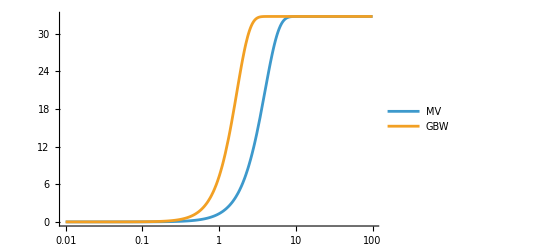

```mathematica
LogLinearPlot[{mv[r],gbw[r]} , {r,10^-2, 100}, PlotLegends->{"MV", "GBW"}]
```

```mathematica
ir[r_] := Exp[-0.4 r^2];
fbmv[p_, q_, a_,b_,c_,d_] := NIntegrate[mv[r]r BesselJ[a,  p r] BesselK[b, q r] (p r)^c(q r)^d ir[r], {r,10^-6, 1/Λ}];
fbgbw[p_, q_, a_,b_,c_,d_] := NIntegrate[gbw[r]r BesselJ[a,  p r] BesselK[b, q r] (p r)^c(q r)^d ir[r], {r,10^-6, 1/Λ}];
```

```mathematica
pstep =0.05;
qstep = 0.05;
datamv = Table[{p, q,Log[Abs[fbmv[p, q,0,0,0,0]]]}, {p, 0.5, 5,pstep}, {q,0.1, 4,qstep}];
datagbw = Table[{p, q,Log[Abs[fbgbw[p, q,0,0,0,0]]]}, {p, 0.5, 5,pstep}, {q,0.1, 4, qstep}];
```

```mathematica
<<MaTeX`
```

```mathematica
(*PlotLabel->MaTeX["{N_{\\mathrm{MV}}}^{(00)}_{(00)} ( p_{\\perp}, \\overline{Q})", Magnification->2]*)
mvplot = ListContourPlot[Flatten[datamv,1], 
Contours->50, ContourStyle->None, 
ImageSize->Medium,
 FrameLabel->{MaTeX["p_\\perp \\,\\,\\,[\\mathrm{GeV}]", Magnification->1.5], MaTeX["\\overline{Q}\\,\\,\\,[\\mathrm{GeV}]", Magnification->1.5]},
FrameTicks->{{Automatic,Automatic},{Automatic,None}},
(*GridLines->Automatic,*)
PlotLabel->MaTeX["\\ln |{N_{\\mathrm{MV}}}^{(00)}_{(00)} ( p_{\\perp}, \\overline{Q})|", Magnification->2],
LabelStyle->{Black,18,FontFamily->"Times New Roman"},
PlotLegends->Automatic
];
gbwplot = ListContourPlot[Flatten[datagbw,1], Contours->50, ContourStyle->None, 
ImageSize->Medium,
 FrameLabel->{MaTeX["p_\\perp \\,\\,\\,[\\mathrm{GeV}]", Magnification->1.5], MaTeX["\\overline{Q}\\,\\,\\,[\\mathrm{GeV}]", Magnification->1.5]},
(*GridLines->Automatic,
GridLinesStyle->Directive[Black,Thin],*)
PlotLabel->MaTeX["\\ln | {N_{\\mathrm{GBW}}}^{(00)}_{(00)} ( p_{\\perp}, \\overline{Q}) | ", Magnification->2],
LabelStyle->{Black,18,FontFamily->"Times New Roman"},
PlotLegends->Automatic
];
(*gr =Row[{mvplot,gbwplot}]*)
(*gr = GraphicsRow[{mvplot,gbwplot},Spacings->Scaled[0.005],Alignment->Top]*)
gr=GraphicsRow[{Style[mvplot,ShowStringCharacters->False],Style[gbwplot,ShowStringCharacters->False]},Spacings->Scaled[0.01],Alignment->Top,ImageSize->900]
(*GraphicsRow[{mvplot,gbwplot},ImageSize->All,Alignment->Bottom,Spacings->Scaled[-1]]*)
(*ResourceFunction["PlotGrid"][{{mvplot,gbwplot}}]*)
(*GraphicsGrid[{{mvplot},{gbwplot}},Spacings->{0,0}]*)

Export["/Users/brandonmanley/Desktop/PhD/oam_pheno/dijet_DSA/plots/sinsin_node.png", gr, ImageResolution->700]
```

-Graphics-

/Users/brandonmanley/Desktop/PhD/oam_pheno/dijet_DSA/plots/sinsin_node.png

/Users/brandonmanley/Desktop/PhD/oam_pheno/dijet_DSA/plots/sinsin_node.pdf